```mathematica
tocher[z_] := 1/(1+Exp[-2*Sqrt[2/(Pi*z)]])
```

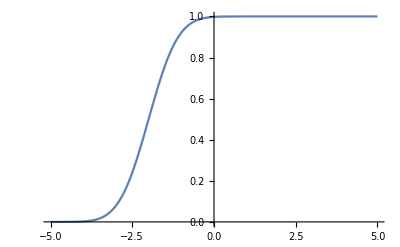

```mathematica
Plot[approx[(x+2)/Sqrt[0.5]],{x,-5,5}]
```

```mathematica
approx[z_] := 1/(1+Exp[-1.5976*z-0.07056(z^3)])
```

```mathematica
transformApprox[z_,mu_,sigma_]:=approx[(z+mu)/Sqrt[sigma]]
```

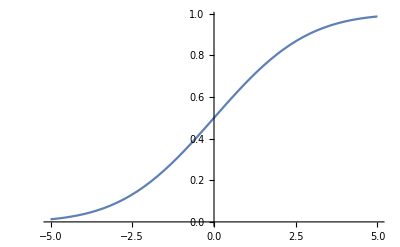

```mathematica
Plot[transformApprox[x,0,5],{x,-5,5}]
```

```mathematica
<<"/home/denpak/Applications/Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
CS1=DynamicalSystem[{-x^3+alpha x+beta} ,{{x,-5,5}},{{beta,-5,5},{alpha,-5,5}}]
```

DynamicalSystem[«1 ODE»,{x},{beta,alpha}]

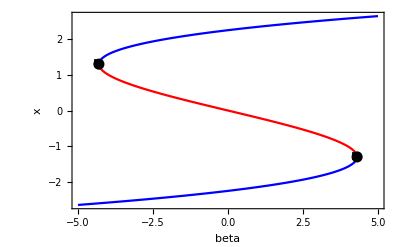

```mathematica
DisplayBifurcationDiagram[CS1/.alpha->5,beta,MaxStepSize->0.1]
```

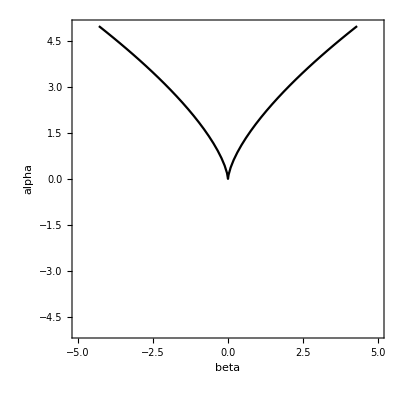

```mathematica
DisplayParameterChart[CS1,{beta,alpha}]
```

DynamicalSystem[«1 ODE»,{x},{alpha→1,beta→0}]

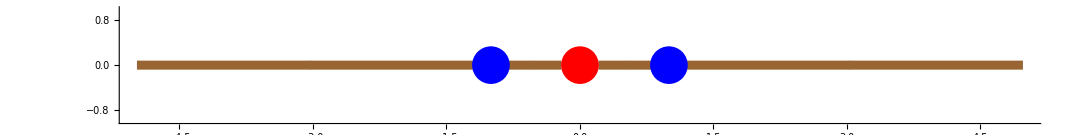

```mathematica
cs = CS1/.{beta->0,alpha->1}
Show[DisplayFlow[cs,1],DisplayPhasePortrait[cs]]
```

```mathematica
$PhasePortraitEPs[[2]]
```

EquilibriumPoint[Unstable,Node,{0}]

```mathematica
cs = CS1/.{beta->2,alpha->5}
boundary=EquilibriumPoints[cs][[2]][[3]][[1]]
transformApprox[boundary,0,0.5]
```

DynamicalSystem[«1 ODE»,{x},{alpha→5,beta→2}]

-0.414214

0.278878

```mathematica
getDistro[c_,d_,mu_:0,sigma_:0.5]:= 
Module[{cs,b},
cs =  CS1/.{alpha->d,beta->c};
b= EquilibriumPoints[cs][[2]][[3]][[1]];
transformApprox[b,mu,sigma]
]
```

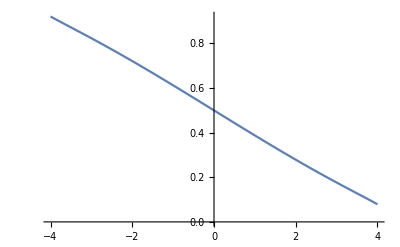

```mathematica
Plot[getDistro[c,5],{c,-4,4}]
```

```mathematica
bf = Plot3D[{getDistro[c,d],.7},{c,-4,4},{d,0,4},MaxRecursion->7,PlotPoints->100,PlotStyle->Opacity[0.5],Mesh->{{0}},MeshFunctions->{#3&},MeshStyle->{Red}]
```

Part::partw: Part 2 of {EquilibriumPoint[Stable,Node,{-1.5874}]} does not exist.

Part::partw: Part 3 of {EquilibriumPoint[Stable,Node,{-1.5874}]}⟦2⟧ does not exist.

Part::partw: Part 2 of {EquilibriumPoint[Stable,Node,{-1.5874}]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

```mathematica
plane = Plot3D[.7, {c,-4,4},{d,0,4},PlotStyle->Opacity[0.5],Mesh->{{0}},MeshFunctions->{#3&},MeshStyle->{Red}]
```

-Graphics3D-

```mathematica
Show[bf,plane]
```

-Graphics3D-

```mathematica
Plot3D[{getDistro[c,d],.7},{c,-2,1},{d,0,4},PlotStyle->Opacity[0.5],Mesh->{{0}},MeshFunctions->{#3&},MeshStyle->{Red},MaxRecursion->7]
```

Part::partw: Part 2 of {EquilibriumPoint[Stable,Node,{-1.25995}]} does not exist.

Part::partw: Part 3 of {EquilibriumPoint[Stable,Node,{-1.25995}]}⟦2⟧ does not exist.

Part::partw: Part 2 of {EquilibriumPoint[Stable,Node,{-1.25995}]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["/home/denpak/Research/Alife2023/pg.png",%49,"PNG"]
```

/home/denpak/Research/Alife2023/pg.png

```mathematica
Export["/home/denpak/Research/Alife2023/pg.png",%49,"PNG"]
```

/home/denpak/Research/Alife2023/pg.png